```mathematica
LT[f_,t_,s_]:=∫_(-∞)^∞ f ⅇ^(-s t)ⅆt
```

```mathematica
f[t_]:=Piecewise[{{1,-3<t<4}}]
```

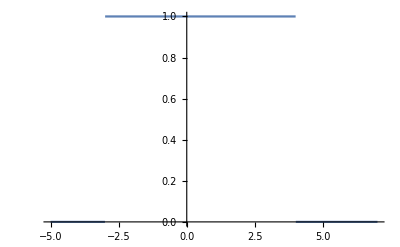

```mathematica
Plot[f[t],{t,-5,7}]
```

```mathematica
F=LT[f[t],t,s]
```

(ⅇ^(-4 s) (-1+ⅇ^(7 s)))/s

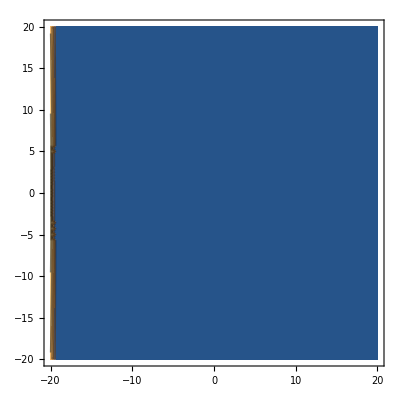
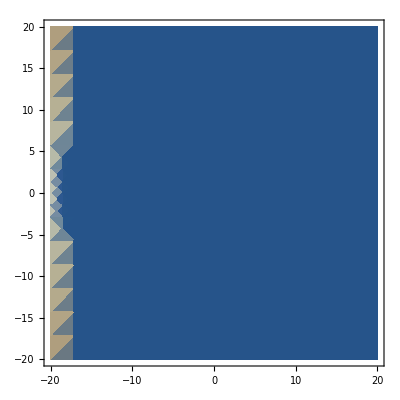
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{s=σ+I ω},Table[plot[Abs[F],{σ,-20,20},{ω,-20,20},PlotRange->Full],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```